# Examples of Rotating Coordinate Systems

## Example 1

A turntable spins with angular velocity Ω in the +z direction. A bee flies past at constant velocity with its position given by (vt,y0,0). Find the position, velocity, and acceleration of the bee as a function of time, as measured by an observer on the turntable.

```mathematica
Clear["`*"]
```

We call the lab S0 and the turntable S. To convert from turntable to lab coordinates, we need to use the rotation matrix R. {lab vector}=R{turntable vector} or {turntable vector}=R inverse{lab vector}.

```mathematica
R={{Cos[Ω t],-Sin[Ω t],0},{Sin[Ω t],Cos[Ω t],0},{0,0,1}};Print[MatrixForm[R]]
RI={{Cos[Ω t],Sin[Ω t],0},{-Sin[Ω t],Cos[Ω t],0},{0,0,1}};Print[MatrixForm[RI]]
Prod=FullSimplify[R.RI];Print[MatrixForm[Prod]]
```

(Cos[t Ω] | -Sin[t Ω] | 0
Sin[t Ω] | Cos[t Ω] | 0
0 | 0 | 1)

(Cos[t Ω] | Sin[t Ω] | 0
-Sin[t Ω] | Cos[t Ω] | 0
0 | 0 | 1)

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

First we find r in S by using the rotation vector, and we differentiate it to find the velocity and acceleration.

```mathematica
r0={v t,y0,0};
r=RI.r0;Print[MatrixForm[r]]
vsA=D[r,t];Print[MatrixForm[vsA]]
asA=D[vsA,t];Print[MatrixForm[asA]]
```

(t v Cos[t Ω]+y0 Sin[t Ω]
y0 Cos[t Ω]-t v Sin[t Ω]
0)

(v Cos[t Ω]+y0 Ω Cos[t Ω]-t v Ω Sin[t Ω]
-t v Ω Cos[t Ω]-v Sin[t Ω]-y0 Ω Sin[t Ω]
0)

(-t v Ω^2 Cos[t Ω]-2 v Ω Sin[t Ω]-y0 Ω^2 Sin[t Ω]
-2 v Ω Cos[t Ω]-y0 Ω^2 Cos[t Ω]+t v Ω^2 Sin[t Ω]
0)

Now we find v and a by the formulas.Note that the right hand sides are in terms of S0 unit vectors, so we need to rotate back to S to get the correct answers. Note the cross product of a and b is CrossProduct[a,b] or a ESC cross ESC b.

```mathematica
Ωvec={0,0,Ω};
vs0=D[r0,t]- Ωvec×r0;Print[MatrixForm[vs0]]
vs=RI.vs0;Print[MatrixForm[vs]]
as0=-2Ωvec×D[r0,t]+Ωvec×(Ωvec×r0);Print[MatrixForm[as0]]
as=RI.as0;Print[MatrixForm[as]]
```

(v+y0 Ω
-t v Ω
0)

((v+y0 Ω) Cos[t Ω]-t v Ω Sin[t Ω]
-t v Ω Cos[t Ω]-(v+y0 Ω) Sin[t Ω]
0)

(-t v Ω^2
-2 v Ω-y0 Ω^2
0)

(-t v Ω^2 Cos[t Ω]+(-2 v Ω-y0 Ω^2) Sin[t Ω]
(-2 v Ω-y0 Ω^2) Cos[t Ω]+t v Ω^2 Sin[t Ω]
0)

Let' s check to see if the results agree :

```mathematica
check1=Simplify[vsA-vs]
check2=Simplify[asA-as]
```

{0,0,0}

{0,0,0}

In this problem, we have solved for the force in the turntable frame. Since there is no (net) real force, this represents the fictitious force that would be necessay to produce the spiral motion of the bee if the turntable were an inertial frame. 
Let's plug in some numbers and plot the results.

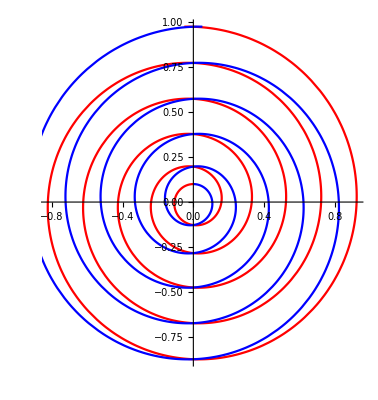

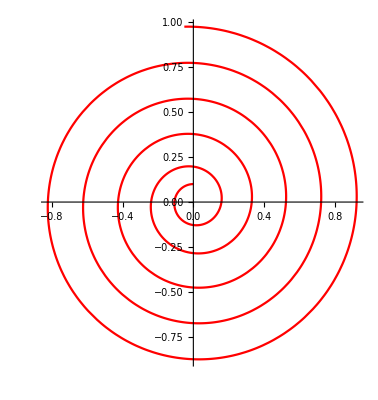

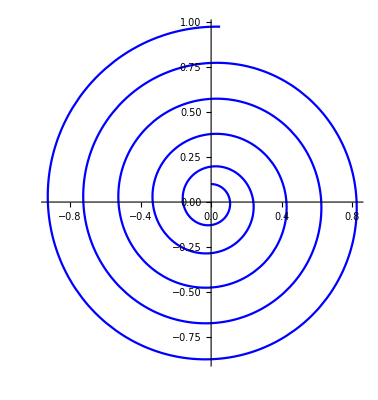

```mathematica
y0=0.1;
Ω=100;
v=3.24;
P1=ParametricPlot[{r[[1]],r[[2]]},{t,-0.3,0},PlotStyle->Red];
P2=ParametricPlot[{r[[1]],r[[2]]},{t,0,+0.3},PlotStyle->Blue];
Show[P1,P2]
Show[P1]
Show[P2]
(*{r[1],r[2],{t=0..0.3},
plot([r[1],r[2],t=0..0.3],scaling=constrained);
plot([vs[1],vs[2],t=0..0.3],scaling=constrained);
plot([as[1],as[2],t=0..0.3],scaling=constrained);*)
```

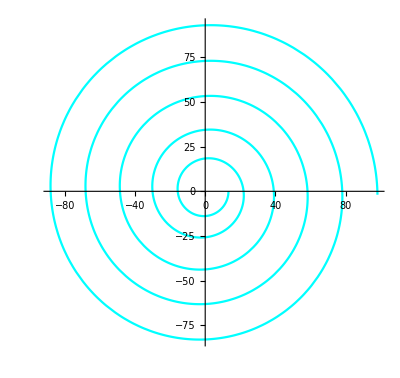

```mathematica
ParametricPlot[{vs[[1]],vs[[2]]},{t,0,0.3},PlotStyle->Cyan]
```

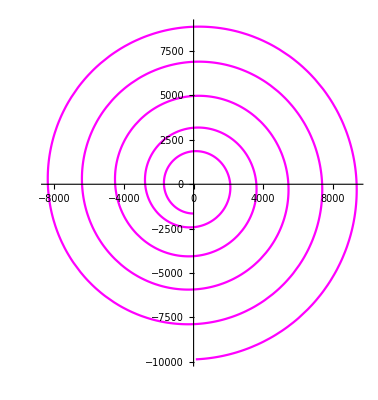

```mathematica
ParametricPlot[{as[[1]],as[[2]]},{t,0,0.3},PlotStyle->Magenta]
```

## Example 2

A nickel is at rest on a rotating turntable. Find the force that holds the nickel in place.

```mathematica
Clear["`*"]
```

```mathematica
R={{Cos[Ω t],-Sin[Ω t],0},{  Sin[Ω t],Cos[Ω t],0},{0,0,1}};
RI={{Cos[Ω t],Sin[Ω t],0},{-Sin[Ω t],Cos[Ω t],0},{0,0,1}};
```

We know that the nickel is at a fixed location on the turntable - S.Let' s just call this x0.From there, we rotate to get into the lab, S0.We can differentiate to find the total true acceleration from there.

```mathematica
r={x,0,0};Print[MatrixForm[r]]
r0=R.r;Print[MatrixForm[r0]]
vs0A=D[r0,t];Print[MatrixForm[vs0A]]
as0A=D[vs0A,t];Print[MatrixForm[as0A]]
```

Now we apply the equations. We know r and we know that v and a are zero.

```mathematica
Ωvec={0,0,Ω};
as0=Ωvec×(Ωvec×r0);
Print[MatrixForm[as0]]
check=as0-as0A;Print[MatrixForm[check]];
```

We have solved for the force in the lab frame, so this is the real force that holds the nickel in a circular path.This force is just F = ma = -m Ω^2 r.